To find the magnetic field profile in the boundary layer, one needs to solve the equation
	B_z'(x) = -(4π)/c J_y (x).
So, employing the distribution function
	f(v,θ)=n_0/(2 π v_th^2)exp(- v^2/(2 v_th^2))  H (v - (v sin(θ) + G(x))) ,		G(x)=e/mc ∫ B(ξ)ⅆξ
we have to calculate
	J_y (x) = ∫∫ e f(v, θ) v sin(θ) * vⅆvⅆθ ,
	n (x) = ∫∫  f(v, θ) * vⅆvⅆθ .

To integrate Heaviside theta-function we’ll use the technique found
 with the simpler distribution function
 	f(v,θ)=n_0/(2 π V)δ(v- V)  H (v - (v sin(θ) + G(x))) . 
 For one particular velocity V,
	∫_-π^π V sin(θ) H (V - (V sin(θ) + G(x))) ⅆθ  = 2∫_(arcsin(-1 + G/V))^(π/2) V sin(θ) ⅆθ .

```mathematica
Integrate[2 V Sin[θ],{θ, ArcSin[-1+G/V], π/2}, Assumptions->{V>0, G∈Reals}] // FullSimplify
```

2 √(-G (G-2 V))

Now, we can integrate found quantities with the new distribution function.
To do so, we substitute V→x v_th, G -> g v_th and multiply them by the gaussian exponent.

```mathematica
Jy[g_] := Integrate[x ⅇ^(-x^2/2) Sqrt[g (2x-g)], {x,g/2, ∞},Assumptions->g∈Reals] 
Jy[g]
```

ConditionalExpression[(ⅇ^(-g^2/16) g BesselK[-1/4,g^2/16])/(2 √2), g>0]

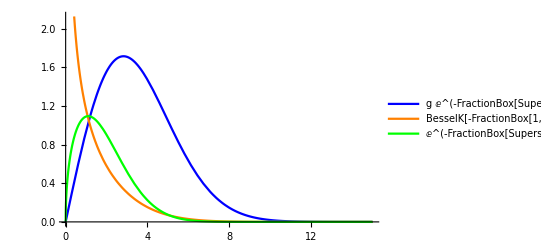

```mathematica
Plot[{g ⅇ^(-g^2/16),BesselK[-1/4,g^2/16]/(2 √2),(ⅇ^(-g^2/16) g BesselK[-1/4,g^2/16])/(2 √2)} , {g, 0, 15}, PlotLegends->{"g ⅇ^(-FractionBox[SuperscriptBox[g, 2], 16])","BesselK[-FractionBox[1, 4], FractionBox[SuperscriptBox[g, 2], 16]]/(2 SqrtBox[2])", "ⅇ^(-FractionBox[SuperscriptBox[g, 2], 16])/(2 SqrtBox[2])"},
PlotStyle->{Blue, Orange, Green}]
```

```mathematica
Series[Jy[g], g->0]
```

ConditionalExpression[(Gamma[1/4] √g)/(2 2^(1/4))+O[g]^(3/2), g>0]